```mathematica
g1=Show[Plot[PDF[NormalDistribution[70,9],x],{x,30,110},PlotStyle->{Gray,Thickness[0.01]},AxesLabel->{"Test score",pdf},BaseStyle->{FontSize->16}],Plot[PDF[NormalDistribution[70,9],x],{x,90,110},Filling->Axis],ImageSize->Large];
```

```mathematica
g2 = Show[Plot[CDF[NormalDistribution[0,1],x],{x,-4,4},PlotStyle->{Gray,Thickness[0.01]},AxesLabel->{"Standardised test score",cdf},BaseStyle->{FontSize->16}],ImageSize->Large];
```

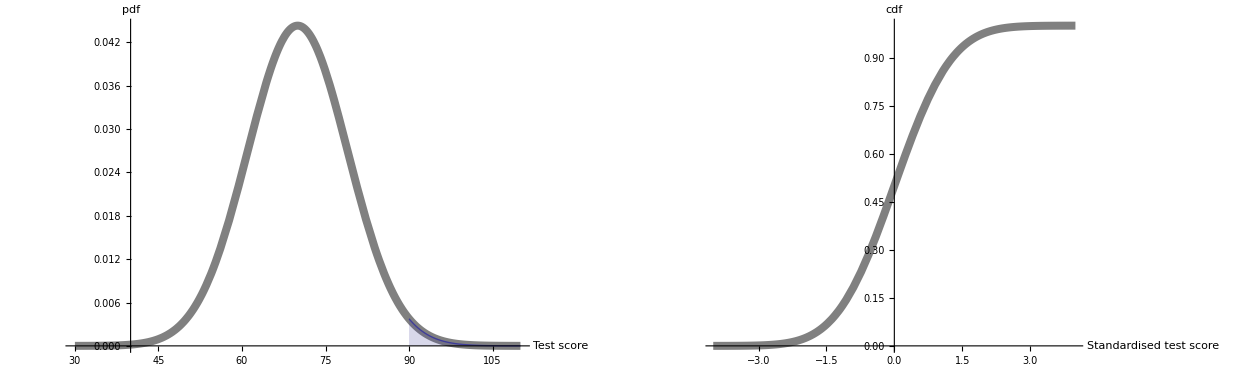

```mathematica
GraphicsRow[{g1,g2}]
```